# Learning Mathematica

## Lecture 5

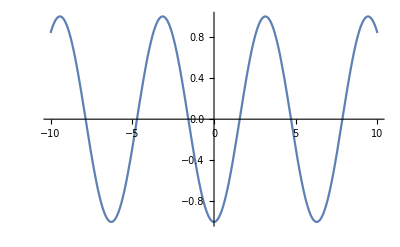

```mathematica
Plot[{-Cos[x]}, {x, -10, 10}]
```

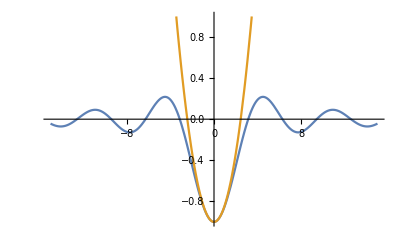

```mathematica
Plot[{-Sin[x]/x, -1+x^2/6},{x, -15, 15}, PlotRange->{-1, 1}]
```

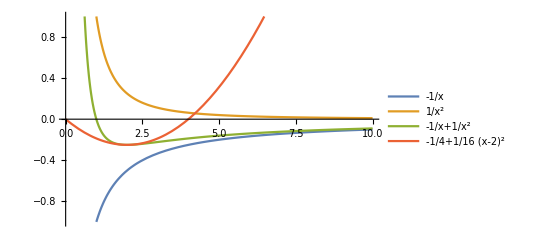

```mathematica
Plot[{-1/x,1/x^2, -1/x+1/x^2, -1/4+ 1/16(x-2)^2}, {x, 0, 10}, PlotLegends->"Expressions", PlotRange->{-1, 1} ]
```

## Lecture 6

### Function behavior near x = 0

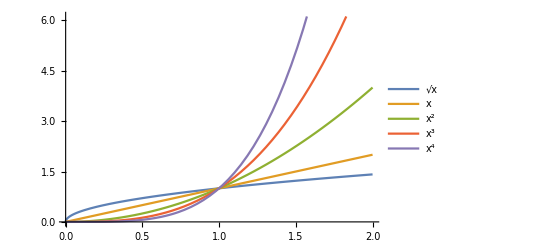

```mathematica
Plot[{Sqrt[x], x, x^2, x^3, x^4}, {x, 0, 2}, PlotLegends-> "Expressions"]
```

# Radicals and Logarithms

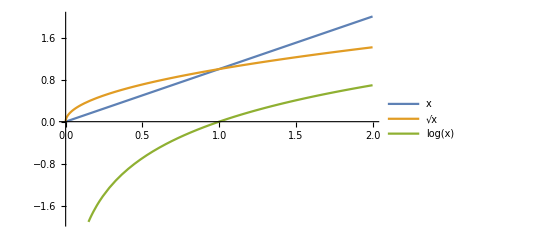

```mathematica
Plot[{x, Sqrt[x], Log[x]}, {x, 0, 2}, PlotLegends->"Expressions"]
```

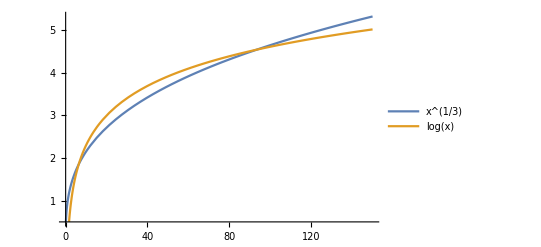

```mathematica
Plot[{x^(1/3), Log[x]}, {x,0, 150}, PlotLegends->"Expressions"]
```

```mathematica
Manipulate[Plot[1/(x^2- a^2), {x, -5, 5}, PlotRange -> Full, PlotLabel->Style["a" -> a, 16, Red]] ,{a, -10, 10} ]
```

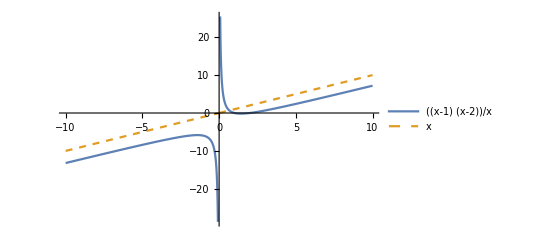

```mathematica
Plot[{(x-1)(x-2)/x, x},{ x, -10, 10}, PlotLegends->"Expressions", PlotStyle->{Thick, Dashed}]
```

```mathematica
Manipulate[Plot[{Exp[-x^2/a^2], Exp[1]}, {x, -5, 5}, PlotRange->Full, PlotLabel->Style["a"->a, 16, Black], PlotLegends->{"Gaussian", "1/e^-1"}], {a, -5,5}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

# Lecture 8 (Vector Fields)

## Q1

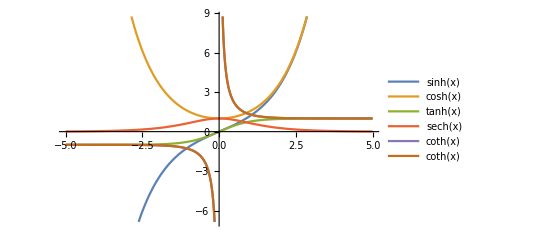

```mathematica
Plot[{Sinh[x], Cosh[x], Tanh[x], Sech[x], Coth[x], Coth[x]}, {x, -5, 5}, PlotLegends->"Expressions"]
```

## Q2

```mathematica
Manipulate[Plot[{Sinh[a x], Sech[a x], Tanh[a x], Coth[a x]}, {x, -5, 5}, PlotLegends->"Expressions"], {a, -10, 10}]
```

## Q3

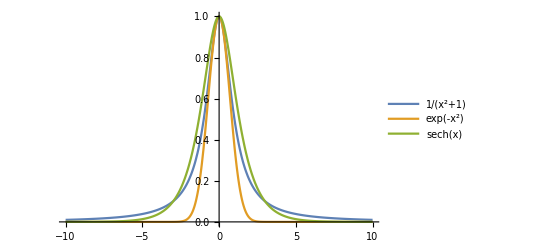

```mathematica
Plot[{1/(x^2+1), Exp[-x^2], Sech[x]}, {x, -10, 10}, PlotLegends->"Expressions", PlotRange->Full]
```

## Vector Fields